```mathematica
ClearAll["Global`*"]
```

```mathematica
F[x_,y_,a_,b_]:=(a*x+b*y)^2/1+(-b*x+a*y)^2/2^2
```

```mathematica
Manipulate[Plot3D[F[x,y,a,b],{x,-1000,1000},{y,-1000,1000}],{a,0.1,2},{b,0.1,2}]
```

```mathematica
Manipulate[ContourPlot[(a*x+b*y)^2/1+(-b*x+a*y)^2/2^2,{x,-20,20},{y,-20,20}],{a,-2,2},{b,-2,2}]
```

```mathematica
c0:=4(*Centre of the elliples*)
```

```mathematica
r:=2 (*radius of domain of Elliples*)
```

```mathematica
R:=8 (*radius of domain of defn*)
```

```mathematica
ℛ1=ImplicitRegion[(x-c0)^2+y^2<=r^2,{x,y}];
```

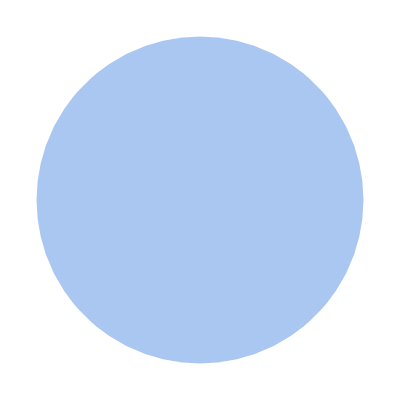

```mathematica
Region[ℛ1]
```

```mathematica
ℛ2=ImplicitRegion[(x+c0)^2+y^2<=r^2,{x,y}];
```

```mathematica
Region[ℛ2]
```

-Graphics-

```mathematica
ℛ3=ImplicitRegion[x^2+y^2<=R^2,{x,y}];
```

```mathematica
Region[ℛ3]
```

-Graphics-

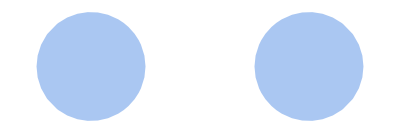

```mathematica
Region[RegionUnion[ℛ2,ℛ1]]
```

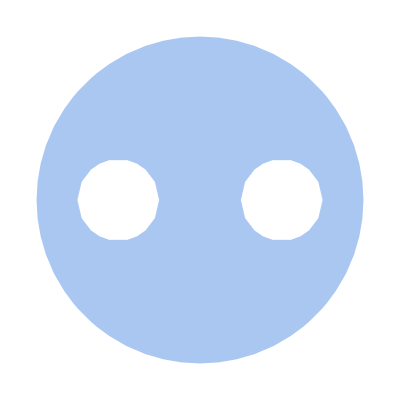

```mathematica
Region[RegionDifference[ℛ3,RegionUnion[ℛ2,ℛ1]]]
```

```mathematica
F1[x_,y_,a_,b_]:=Piecewise[{{(a*(x-c0)+b*y)^2/1+(-b*(x-c0)+a*y)^2/2^2,{x,y} ∈ℛ1},{(a*(x+c0)+b*y)^2/1+(-b*(x+c0)+a*y)^2/2^2,{x,y} ∈ℛ2},{2,{x,y} ∈RegionDifference[ℛ3,RegionUnion[ℛ2,ℛ1]]}}]
```

```mathematica
Manipulate[ContourPlot[Piecewise[{{(a*(x-c0)+b*y)^2/1+(-b*(x-c0)+a*y)^2/2^2,{x,y} ∈ℛ1},{(-b*(x+c0)+a*y)^2/1+(a*(x+c0)+b*y)^2/2^2,{x,y} ∈ℛ2}},2],{x,y}∈ℛ3],{a,-2,2},{b,-2,2}]
```

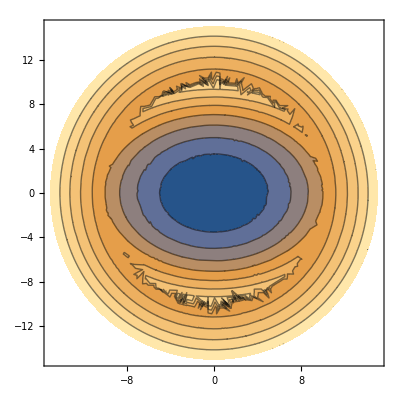

```mathematica
ContourPlot[Piecewise[{{x^2+2*y^2,{x,y}∈ImplicitRegion[x^2+y^2<=10^2,{x,y}]}},x^2+1*y^2],{x,y}∈ImplicitRegion[x^2+y^2<=15^2,{x,y}]]
```

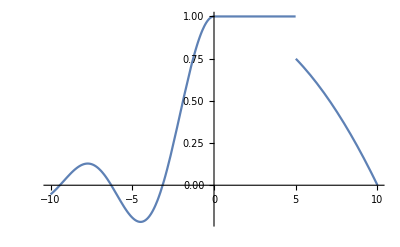

```mathematica
Plot[Piecewise[{{Sin[x]/x,x<0},{1,0<=x<=5}},-x^2/100+1],{x,-10,10}]
```

```mathematica
(*Touching plane changes with temperature*)
```

```mathematica
a[x_,y_]:=1+Abs[x]^2
```

```mathematica
b[x_]:=Piecewise[{{1+0.001*Abs[x],0<=Abs[x]<=10},{(Abs[x]-10)^2+0.001*10+1,10<=Abs[x]<=20}},1]
```

```mathematica
G1[x_,y_]:=(x/a[x,y])^2+(y/b[y])^2(*((x+y)/a[x,y])^2+((x-y)/b[x])^2*)
```

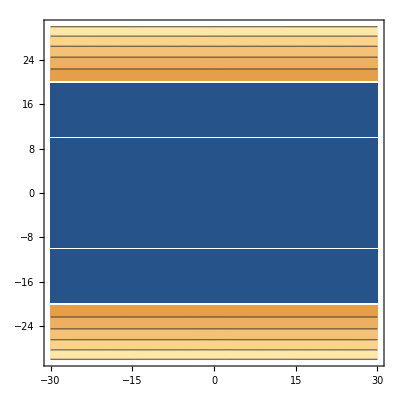

```mathematica
ContourPlot[G1[x,y],{x,-30,30},{y,-30,30}]
```

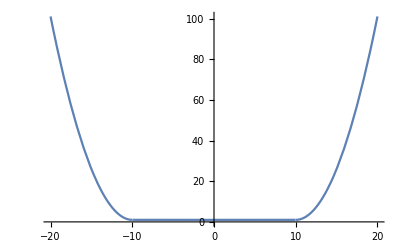

```mathematica
Plot[b[x],{x,-20,20}]
```

```mathematica
Manipulate[Plot[c*x-a*x^2+b*x^4,{x,-20,20}],{a,0,100},{b,0,1},{c,0,150}]
```

```mathematica
(*Function to plot the convex hull of a function*)
```

```mathematica
ConvexHullFunction[f_,a_,b_]:=Module[{top,g,R,poly,pickers,plist,pts},g=Plot[f[x],{x,a,b}];
pts=Join@@Cases[g,_Line,All][[All,1]];
top=Max[pts[[All,2]]];
R=ConvexHullMesh[Join[{{a,top+1}},pts,{{b,top+1}}]];
poly=MeshCells[R,2][[1,1]];
pickers=Range[MeshCellCount[R,0]] UnitStep[Subtract[top+0.5,MeshCoordinates[R][[All,2]]]];
plist=DeleteCases[pickers[[poly]],0];
pts=SortBy[MeshCoordinates[R][[plist]],First];
Interpolation[pts,InterpolationOrder->1]]
```

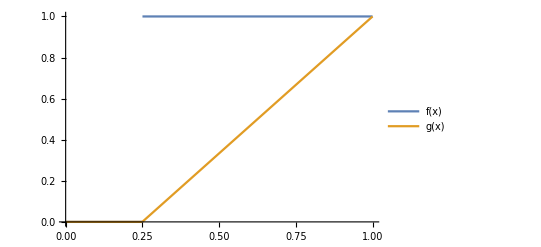

```mathematica
f=r↦Piecewise[{{1,r>0.25},{0,r>0&&r<0.25}}];
a=0;
b=1;
g=ConvexHullFunction[f,a,b];
Plot[{f[x],g[x]},{x,a,b},PlotLegends->"Expressions"]
```

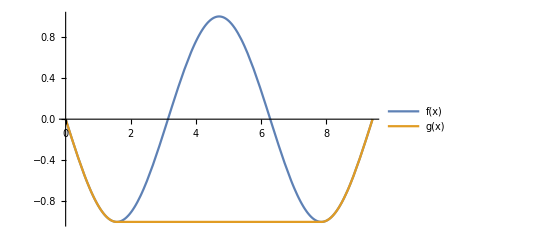

```mathematica
f=x↦-Sin[x];
a=0;
b=3 Pi;
g=ConvexHullFunction[f,a,b];
plot=Plot[{f[x],g[x]},{x,a,b},PlotLegends->"Expressions"]
```

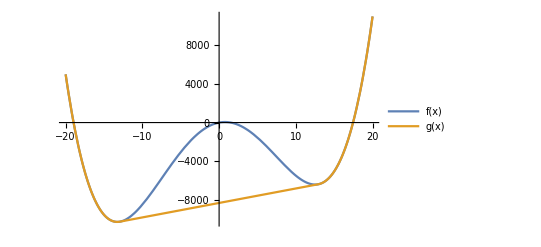

```mathematica
f=x↦150*x-100*x^2+0.3*x^4;
xL=-20;
xR=20;
g=ConvexHullFunction[f,xL,xR];
h=D[g[x],x];
e = D[f[x],x];
plot=Plot[{f[x],g[x]},{x,xL,xR},PlotLegends->"Expressions"]
```

```mathematica
Plot3D[g[x]*y^2,{x,xL,xR},{y,-20,20}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[(c*x-a*x^2+b*x^4)*y^2,{x,-20,20},{y,-10,10}],{a,0,100},{b,0,1},{c,0,100}]
```